## Общие функции и точности

```mathematica
f[{x_,y_}]:=6 x^2+3 y^2-4x y+4 √5(x+2y)+22;
rosenbrok[{x_,y_}]:=(1-x)^2+(y-x^2)^2;
```

# Метод сопряженных направлений

```mathematica
ConjDirections[x_] := Module [
{
p,
step,
norms = {},

},
4
];
```

# Алгоритм Флетчера-Ривса

```mathematica
FletcherRivs[{x0_, y0_},func_,ϵ_ ] :=Module [
{
point = {x0, y0},
points = {},
step = 0,
norms = {},
direction,
criteria,
κ,
ω,
funcpoints = {},
funcpoint,
funcprevpoint
},
points = {point};
direction = -Grad[func[{x,y}],{x,y}]/.{x->point[[1]],y->point[[2]]};
criteria = ϵ + 1;
While[criteria ≥ ϵ,
AppendTo[norms, Norm@direction];
κ = NArgMin[func[point + α*direction],α];
point = point + κ* direction;
points = AppendTo[points, point];
ω= ( Norm@Grad[func[{x,y}],{x,y}]/.{x->point[[1]],y->point[[2]]})^2/( Norm@Grad[func[{x,y}],{x,y}]/.{x->points[[Length@points - 1]][[1]],y->points[[Length@points - 1]][[2]]})^2;
direction = ω * direction -Grad[func[{x,y}],{x,y}]/.{x->point[[1]],y->point[[2]]};
funcprevpoint = func[points[[Length@points - 1]]];
funcpoint = func[point];
funcpoints = AppendTo[funcpoints, funcprevpoint];
funcpoints = AppendTo[funcpoints, funcpoint];
criteria = Norm[-funcprevpoint + funcpoint];
] ;
{points, funcpoints, norms}
];
```

```mathematica
func = rosenbrok;
FR = FletcherRivs[{0, 1}, func, 0.01];
setX = {x,-2,2};
setY ={y,-6,4};
```

```mathematica
func = f;
FR = FletcherRivs[{0, 1}, func, 0.01];
setX = {x,-4,0};
setY ={y,-8,0};
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

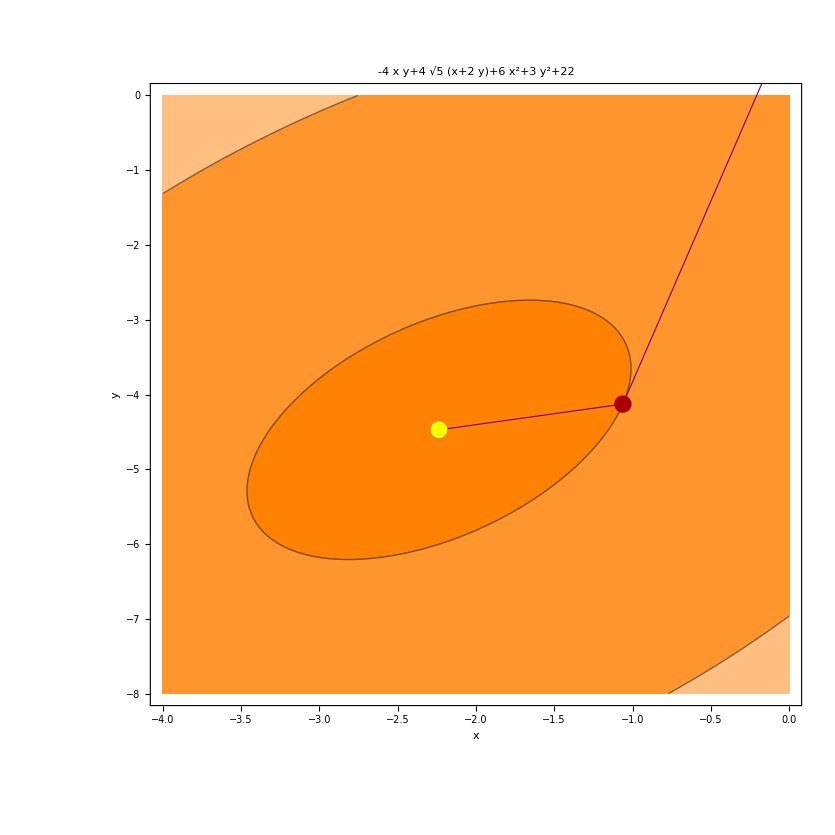

```mathematica
ContourPlot[func[{x,y}],setX,setY,Contours->FR[[2]],ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{func[{x,y}]}]],FrameStyle->Thick,ImageSize->350,PlotPoints->100,Epilog->{Purple,Thickness[0.001],Arrowheads[.02],Table[Arrow[FR[[1]][[i-1;;i]]],{i,2,Length[FR[[1]]]}],Darker[Red],PointSize[0.015],Point[FR[[1]][[1;;-1]]],Yellow,Point[FR[[1]][[-1]]]}]
```

```mathematica
FR[[2]]
```

27.6374